Noanah Malati

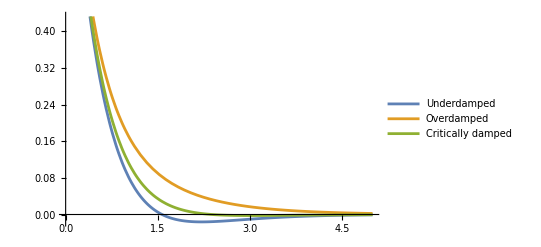

```mathematica
x0=1;dx0=-2;tf=5;
sol1=NDSolve[{2x''[t]+6x'[t]+5x[t]==0,x[0]==x0,x'[0]==dx0},x[t],{t,0,tf}];
sol2=NDSolve[{2x''[t]+7x'[t]+5x[t]==0,x[0]==x0,x'[0]==dx0},x[t],{t,0,tf}];
sol3=NDSolve[{2x''[t]+√40 x'[t]+5x[t]==0,x[0]==x0,x'[0]==dx0},x[t],{t,0,tf}];
Plot[{Evaluate[x[t]]/.sol1,Evaluate[x[t]]/.sol2,Evaluate[x[t]]/.sol3},{t,0,tf},PlotLegends->{"Underdamped","Overdamped","Critically damped"}]
```